C:\Users\Utena\PycharmProjects\Mathematics_in_Chemistry_2018_Spring_Jarren\Assignment2 1D_Quantum_Systems\Morse

10

120

0.185001 (1-ⅇ^(-1.21023 (-1.77993+x)))^2

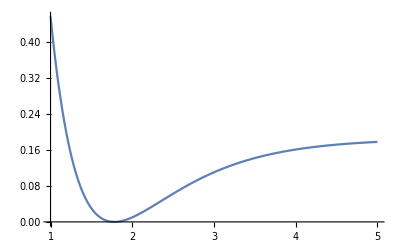

```mathematica
SetDirectory[NotebookDirectory[]]
L=10
Nt=120

potentialFun[x_]=0.001593601*116.09*(1-Exp[-2.287*0.5291772108*(x-0.9419/0.5291772108)])^2
Plot[potentialFun[x],{x,1,L/2}]
```

```mathematica
12
```

12

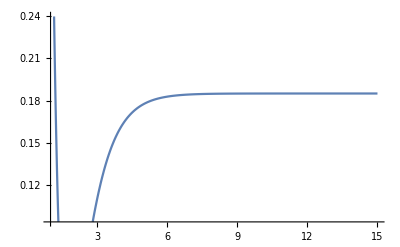

-Graphics-

```mathematica
sinBasis=Table[Sqrt[2/L]Sin[π i (x+L/2)/L],{i,Nt}]
kineticEnerOperator[f_,x_]:=(-D[f,{x,2}])/(2*1728.16)
harmonicOperator[f_,x_]:=kineticEnerOperator[f,x]+potentialFun[x]*f
hamiltonianMatrix=Table[NIntegrate[sinBasis[[m]] harmonicOperator[sinBasis[[n]],x],{x,-L/2,L/2}],{m,Nt},{n,Nt}]

{Energy,Coeff}=Eigensystem[hamiltonianMatrix,-20]
eigxp=Coeff.sinBasis
```

{Sin[1/10 π (5+x)]/(√5),Sin[1/5 π (5+x)]/(√5),Sin[3/10 π (5+x)]/(√5),Sin[2/5 π (5+x)]/(√5),Sin[1/2 π (5+x)]/(√5),Sin[3/5 π (5+x)]/(√5),Sin[7/10 π (5+x)]/(√5),Sin[4/5 π (5+x)]/(√5),Sin[9/10 π (5+x)]/(√5),Sin[π (5+x)]/(√5),Sin[11/10 π (5+x)]/(√5),Sin[6/5 π (5+x)]/(√5),Sin[13/10 π (5+x)]/(√5),Sin[7/5 π (5+x)]/(√5),Sin[3/2 π (5+x)]/(√5),Sin[8/5 π (5+x)]/(√5),Sin[17/10 π (5+x)]/(√5),Sin[9/5 π (5+x)]/(√5),Sin[19/10 π (5+x)]/(√5),Sin[2 π (5+x)]/(√5),Sin[21/10 π (5+x)]/(√5),Sin[11/5 π (5+x)]/(√5),Sin[23/10 π (5+x)]/(√5),Sin[12/5 π (5+x)]/(√5),Sin[5/2 π (5+x)]/(√5),Sin[13/5 π (5+x)]/(√5),Sin[27/10 π (5+x)]/(√5),Sin[14/5 π (5+x)]/(√5),Sin[29/10 π (5+x)]/(√5),Sin[3 π (5+x)]/(√5),Sin[31/10 π (5+x)]/(√5),Sin[16/5 π (5+x)]/(√5),Sin[33/10 π (5+x)]/(√5),Sin[17/5 π (5+x)]/(√5),Sin[7/2 π (5+x)]/(√5),Sin[18/5 π (5+x)]/(√5),Sin[37/10 π (5+x)]/(√5),Sin[19/5 π (5+x)]/(√5),Sin[39/10 π (5+x)]/(√5),Sin[4 π (5+x)]/(√5),Sin[41/10 π (5+x)]/(√5),Sin[21/5 π (5+x)]/(√5),Sin[43/10 π (5+x)]/(√5),Sin[22/5 π (5+x)]/(√5),Sin[9/2 π (5+x)]/(√5),Sin[23/5 π (5+x)]/(√5),Sin[47/10 π (5+x)]/(√5),Sin[24/5 π (5+x)]/(√5),Sin[49/10 π (5+x)]/(√5),Sin[5 π (5+x)]/(√5),Sin[51/10 π (5+x)]/(√5),Sin[26/5 π (5+x)]/(√5),Sin[53/10 π (5+x)]/(√5),Sin[27/5 π (5+x)]/(√5),Sin[11/2 π (5+x)]/(√5),Sin[28/5 π (5+x)]/(√5),Sin[57/10 π (5+x)]/(√5),Sin[29/5 π (5+x)]/(√5),Sin[59/10 π (5+x)]/(√5),Sin[6 π (5+x)]/(√5),Sin[61/10 π (5+x)]/(√5),Sin[31/5 π (5+x)]/(√5),Sin[63/10 π (5+x)]/(√5),Sin[32/5 π (5+x)]/(√5),Sin[13/2 π (5+x)]/(√5),Sin[33/5 π (5+x)]/(√5),Sin[67/10 π (5+x)]/(√5),Sin[34/5 π (5+x)]/(√5),Sin[69/10 π (5+x)]/(√5),Sin[7 π (5+x)]/(√5),Sin[71/10 π (5+x)]/(√5),Sin[36/5 π (5+x)]/(√5),Sin[73/10 π (5+x)]/(√5),Sin[37/5 π (5+x)]/(√5),Sin[15/2 π (5+x)]/(√5),Sin[38/5 π (5+x)]/(√5),Sin[77/10 π (5+x)]/(√5),Sin[39/5 π (5+x)]/(√5),Sin[79/10 π (5+x)]/(√5),Sin[8 π (5+x)]/(√5),Sin[81/10 π (5+x)]/(√5),Sin[41/5 π (5+x)]/(√5),Sin[83/10 π (5+x)]/(√5),Sin[42/5 π (5+x)]/(√5),Sin[17/2 π (5+x)]/(√5),Sin[43/5 π (5+x)]/(√5),Sin[87/10 π (5+x)]/(√5),Sin[44/5 π (5+x)]/(√5),Sin[89/10 π (5+x)]/(√5),Sin[9 π (5+x)]/(√5),Sin[91/10 π (5+x)]/(√5),Sin[46/5 π (5+x)]/(√5),Sin[93/10 π (5+x)]/(√5),Sin[47/5 π (5+x)]/(√5),Sin[19/2 π (5+x)]/(√5),Sin[48/5 π (5+x)]/(√5),Sin[97/10 π (5+x)]/(√5),Sin[49/5 π (5+x)]/(√5),Sin[99/10 π (5+x)]/(√5),Sin[10 π (5+x)]/(√5),Sin[101/10 π (5+x)]/(√5),Sin[51/5 π (5+x)]/(√5),Sin[103/10 π (5+x)]/(√5),Sin[52/5 π (5+x)]/(√5),Sin[21/2 π (5+x)]/(√5),Sin[53/5 π (5+x)]/(√5),Sin[107/10 π (5+x)]/(√5),Sin[54/5 π (5+x)]/(√5),Sin[109/10 π (5+x)]/(√5),Sin[11 π (5+x)]/(√5),Sin[111/10 π (5+x)]/(√5),Sin[56/5 π (5+x)]/(√5),Sin[113/10 π (5+x)]/(√5),Sin[57/5 π (5+x)]/(√5),Sin[23/2 π (5+x)]/(√5),Sin[58/5 π (5+x)]/(√5),Sin[117/10 π (5+x)]/(√5),Sin[59/5 π (5+x)]/(√5),Sin[119/10 π (5+x)]/(√5),Sin[12 π (5+x)]/(√5)}

$Aborted

{{0.190271,0.183552,0.182707,0.177891,0.1724,0.167845,0.160961,0.147534,0.142721,0.134402,0.122448,0.113612,0.0942147,0.0881525,0.0711326,0.0570001,0.0443009,0.0299773,0.0172112,-0.0135826},{{-0.0236475,0.0160143,0.0108721,-0.0179117,-0.00789431,0.0367006,-0.0381094,0.0231578,-0.0272357,0.0577705,-0.0804612,0.0648969,-0.0271826,0.00980035,-0.0253863,0.0421043,-0.0317158,0.0139511,-0.0339001,0.100932,-0.172476,0.206463,-0.212265,0.231081,-0.272859,0.296574,-0.261548,0.180262,-0.101185,0.0461166,0.0114544,-0.0975251,0.18667,-0.221503,0.179299,-0.0978789,0.0275919,0.0244837,-0.0836954,0.149439,-0.175111,0.120179,-0.00778399,-0.0902418,0.12494,-0.109091,0.079918,-0.0437972,-0.0192923,0.101584,-0.147077,0.105164,0.00437658,-0.100771,0.120567,-0.0729509,0.0115885,0.0313237,-0.0626598,0.0863316,-0.0747175,0.00446646,0.0900457,-0.128979,0.0676581,0.0467958,-0.11641,0.0894499,-0.00488528,-0.059847,0.0683291,-0.041446,0.00952582,0.0231842,-0.0577603,0.0686721,-0.0238622,-0.0596893,0.107153,-0.0581435,-0.0548482,0.123605,-0.0742405,-0.0482949,0.121672,-0.0740233,-0.0415139,0.106604,-0.0630246,-0.0338308,0.0837504,-0.047715,-0.0238905,0.0578537,-0.0337742,-0.0106102,0.0327074,-0.02599,0.010536,-0.00186139},{-0.0197654,0.00546648,0.0300589,-0.0446168,0.0242048,-0.00113174,0.00817757,-0.0330565,0.036914,-0.0109527,-0.00899871,-0.0077858,0.0416839,-0.0468874,0.01354,0.0182729,-0.012234,-0.0191051,0.0415172,-0.056808,0.10312,-0.192665,0.275828,-0.288819,0.22606,-0.141073,0.0753248,-0.0121192,-0.0826435,0.191425,-0.246565,0.205519,-0.101712,0.00432482,0.0581791,-0.109901,0.165093,-0.184927,0.120144,0.0141736,-0.13481,0.170079,-0.125802,0.0592213,-0.00347219,-0.0547803,0.122029,-0.154768,0.0993392,0.0302532,-0.143223,0.156013,-0.0737512,-0.0257857,0.0794141,-0.0877661,0.0778816,-0.0480556,-0.0207989,0.10671,-0.13695,0.0620611,0.0715225,-0.150636,0.106959,0.0135677,-0.102503,0.0990947,-0.0343743,-0.0258471,0.0534891,-0.0601269,0.049342,-0.00437107,-0.0671546,0.105891,-0.0536344,-0.0641099,0.138117,-0.083433,-0.0581458,0.147676,-0.092413,-0.0523007,0.139345,-0.0850871,-0.0464708,0.118889,-0.0685694,-0.03895,0.0917087,-0.0498022,-0.0282188,0.0626956,-0.0345242,-0.013325,0.035681,-0.0274611,0.0108718,-0.00187873},{-0.0468896,0.0746706,-0.0912402,0.122153,-0.177999,0.24238,-0.294472,0.331844,-0.360651,0.369763,-0.332209,0.240634,-0.132129,0.0643075,-0.0637482,0.103614,-0.13454,0.133129,-0.115615,0.106747,-0.105122,0.0869513,-0.0404268,-0.0156764,0.0533801,-0.0675153,0.075585,-0.0872622,0.0869636,-0.0547397,-0.00242822,0.0521323,-0.0703391,0.06371,-0.0526746,0.0407119,-0.0130187,-0.0340577,0.0753224,-0.0787543,0.0414273,0.00665617,-0.0356487,0.043361,-0.044438,0.0411135,-0.019102,-0.024963,0.0646993,-0.065229,0.0222777,0.0298185,-0.0528581,0.0408138,-0.016058,-0.00325113,0.0193735,-0.0370303,0.0430979,-0.0187681,-0.0288652,0.0614255,-0.0457997,-0.00737699,0.0510681,-0.0494151,0.0116794,0.0238919,-0.0325353,0.020952,-0.00671384,-0.00597036,0.0214676,-0.032225,0.0197831,0.0175641,-0.0490111,0.0379401,0.0134125,-0.0569641,0.0462925,0.0109763,-0.0573761,0.0457508,0.010335,-0.0521033,0.0390516,0.0103078,-0.0429042,0.0293123,0.00953902,-0.0314949,0.0194187,0.00691903,-0.0193447,0.0114847,0.00182429,-0.00690138,0.0042271,-0.000961286},{0.0197549,-0.0738982,0.145552,-0.185912,0.177798,-0.156321,0.158625,-0.172241,0.153472,-0.0906399,0.0249654,0.0000540043,0.00849164,-0.0096187,-0.0108325,0.022847,-0.00413198,-0.0134995,-0.0246549,0.122285,-0.214797,0.237079,-0.191607,0.130984,-0.0829931,0.0214997,0.0789902,-0.183969,0.221813,-0.164065,0.0586802,0.0267839,-0.0759777,0.117252,-0.156759,0.151144,-0.0638153,-0.0698274,0.161329,-0.156378,0.0837406,-0.00904858,-0.0405473,0.0832988,-0.123377,0.119769,-0.0369528,-0.0882276,0.161647,-0.124336,0.014065,0.0779939,-0.100617,0.0747415,-0.0397625,-0.000633109,0.0593309,-0.111503,0.0981052,0.000409435,-0.115066,0.142628,-0.053583,-0.0716012,0.124257,-0.0747952,-0.013049,0.0638604,-0.062168,0.03821,-0.009857,-0.0304256,0.0735563,-0.0744416,0.00328661,0.0934135,-0.118002,0.0273298,0.101431,-0.137772,0.0375943,0.100943,-0.136777,0.0358627,0.0939645,-0.120794,0.0269831,0.0816213,-0.096288,0.0164183,0.0648344,-0.0691622,0.00863512,0.0448507,-0.0442519,0.00660202,0.0230376,-0.0245684,0.0115742,-0.00228392},{-0.142952,0.276985,-0.378282,0.416444,-0.377688,0.274818,-0.134556,-0.0171963,0.153262,-0.238146,0.241207,-0.167002,0.0671087,-0.00933825,0.0267999,-0.0939499,0.151069,-0.153635,0.103552,-0.037994,-0.00960137,0.036192,-0.0576425,0.0774837,-0.0775525,0.0428826,0.0127353,-0.0558329,0.0666829,-0.054796,0.0388127,-0.0206113,-0.0106003,0.0515969,-0.0760117,0.0599335,-0.011356,-0.0351073,0.0529426,-0.0453989,0.0303576,-0.0133606,-0.0132917,0.0466586,-0.0624773,0.0387312,0.0138893,-0.0558281,0.0565873,-0.023196,-0.0127483,0.0301994,-0.0324731,0.0287137,-0.0153917,-0.0138371,0.0457423,-0.0503093,0.0136995,0.0381827,-0.0598799,0.0322766,0.0176232,-0.0457354,0.0347145,-0.0041019,-0.0182273,0.0239083,-0.0205977,0.0116514,0.00720573,-0.0305315,0.0362164,-0.0083505,-0.0352952,0.0519525,-0.0185993,-0.0366726,0.0584413,-0.0224298,-0.0358773,0.0571545,-0.0209946,-0.0333587,0.0503303,-0.0164683,-0.0292241,0.040394,-0.0111862,-0.023527,0.0295069,-0.00699478,-0.0165636,0.019489,-0.00515777,-0.00875069,0.0116778,-0.00693429,0.00217109,-0.000284961},{0.03455,-0.0261117,-0.0101664,0.0221412,0.00823766,-0.0413557,0.0354508,-0.00367056,-0.00664473,-0.0168601,0.0320149,-0.00207963,-0.0476622,0.058579,-0.0168569,-0.0260946,0.0197418,0.0251075,-0.0640494,0.0891634,-0.134049,0.203831,-0.236369,0.164421,-0.00563962,-0.140966,0.194868,-0.166482,0.116403,-0.0663265,-0.0140578,0.131063,-0.21687,0.188469,-0.0486261,-0.102858,0.168106,-0.140382,0.0803435,-0.0253822,-0.0410622,0.126578,-0.175747,0.117979,0.0340965,-0.169081,0.180509,-0.0732251,-0.0518159,0.109253,-0.0998523,0.0683597,-0.0272409,-0.0423537,0.122972,-0.140713,0.044853,0.107084,-0.182212,0.106227,0.0525709,-0.151301,0.117159,-0.00652304,-0.0752147,0.0838482,-0.0510365,0.0138415,0.0284534,-0.0773659,0.0920402,-0.0262783,-0.0900749,0.146911,-0.0652786,-0.0951162,0.175326,-0.0831289,-0.0961204,0.179851,-0.081843,-0.0940643,0.165952,-0.0676304,-0.0882926,0.13998,-0.0477754,-0.0779971,0.108165,-0.0287317,-0.0629907,0.0758699,-0.0150407,-0.044091,0.0474286,-0.00935843,-0.0225859,0.0253525,-0.0121739,0.00242973},{0.086929,-0.112647,0.0839744,-0.0550797,0.0492931,-0.0312291,-0.0336935,0.116369,-0.147708,0.10121,-0.0257039,-0.014445,0.0114698,-0.00589092,0.01816,-0.0221083,-0.00182047,0.0154421,0.0399103,-0.156023,0.24073,-0.209079,0.0769208,0.0589838,-0.127315,0.140409,-0.140258,0.120098,-0.0368159,-0.102964,0.209891,-0.193147,0.0622587,0.0791473,-0.141533,0.126556,-0.0877515,0.0443605,0.0286346,-0.127445,0.179791,-0.113522,-0.0443016,0.171557,-0.1689,0.0568317,0.0591913,-0.10481,0.0919283,-0.0631666,0.0217796,0.0516277,-0.129442,0.132578,-0.0219074,-0.12715,0.179562,-0.0806099,-0.0795621,0.157135,-0.0995372,-0.0173249,0.0873424,-0.0801084,0.0384009,0.000179612,-0.0392151,0.0793086,-0.0797867,0.00382538,0.105497,-0.138103,0.0353225,0.120115,-0.169808,0.0497581,0.12593,-0.176528,0.0483878,0.124429,-0.163621,0.0364417,0.116234,-0.137877,0.020294,0.101963,-0.106061,0.00555452,0.0827221,-0.0739788,-0.00393195,0.0602466,-0.0461019,-0.00618273,0.0365998,-0.0254044,-0.000558503,0.0121661,-0.00802448,0.00188222},{-0.0118735,-0.0131931,0.0541221,-0.0554449,0.00209144,0.0563357,-0.066096,0.0341909,-0.0114402,0.0193795,-0.0232211,-0.0117359,0.0612869,-0.0684864,0.0229097,0.0182183,-0.000680885,-0.0602739,0.108576,-0.125241,0.139532,-0.159338,0.13268,-0.0135535,-0.149435,0.232994,-0.163631,3.2939×10^-6,0.128995,-0.154417,0.110602,-0.0568294,-0.00160948,0.0867087,-0.167584,0.159857,-0.0272607,-0.144234,0.212241,-0.121935,-0.0390616,0.138057,-0.127716,0.0615948,-0.00106627,-0.0497471,0.103789,-0.125835,0.0578509,0.0852091,-0.187418,0.13882,0.0342386,-0.177703,0.163257,-0.0175412,-0.11631,0.132249,-0.0522515,-0.0312627,0.0662164,-0.0673454,0.0535314,-0.00917719,-0.0696195,0.123165,-0.0733314,-0.0676178,0.170891,-0.114707,-0.0671247,0.195724,-0.130673,-0.0697467,0.19995,-0.124887,-0.0739947,0.187633,-0.104349,-0.0770194,0.163582,-0.0767686,-0.0762755,0.132781,-0.0488846,-0.0703853,0.0998528,-0.0255444,-0.059375,0.0687114,-0.00955745,-0.0443653,0.0423327,-0.00199666,-0.0270584,0.0226828,-0.0028878,-0.00780567,0.00585201,-0.00143933},{-0.196069,0.271145,-0.209033,0.0861526,0.0269229,-0.119694,0.197228,-0.223809,0.152499,-0.00587166,-0.114179,0.123237,-0.0462312,-0.012238,-0.0146234,0.0925707,-0.145384,0.149551,-0.143468,0.151617,-0.136372,0.0486046,0.0884389,-0.178608,0.148743,-0.0283941,-0.0829353,0.118676,-0.0940273,0.0547791,-0.0101909,-0.0568075,0.126937,-0.133845,0.0390259,0.10017,-0.169066,0.109967,0.0189281,-0.108478,0.107892,-0.0532583,-0.000196633,0.0404022,-0.0788258,0.096132,-0.0490232,-0.0589159,0.14431,-0.116368,-0.0165949,0.138258,-0.137889,0.0234369,0.0926649,-0.113999,0.0477456,0.0284326,-0.0603971,0.0551045,-0.0364823,0.0025201,0.0518716,-0.0908646,0.0578921,0.0457614,-0.129474,0.095674,0.0421749,-0.151312,0.112881,0.0428291,-0.157694,0.111672,0.0466127,-0.151263,0.0972046,0.0509537,-0.135248,0.0755079,0.0533305,-0.113186,0.052143,0.0520621,-0.0884913,0.0313011,0.0466932,-0.0642418,0.0156298,0.0377591,-0.0428626,0.0062734,0.0265187,-0.0261538,0.00337971,0.0143783,-0.0152727,0.00747277,-0.00171601,0.0000973074},{-0.185193,0.296662,-0.279324,0.128224,0.0894622,-0.259285,0.290296,-0.178105,0.00433926,0.126757,-0.158288,0.103728,-0.0204835,-0.0300976,0.0104756,0.0750401,-0.171963,0.199855,-0.116034,-0.0330362,0.1402,-0.133695,0.040923,0.0510545,-0.087455,0.0808686,-0.061615,0.0260825,0.0422749,-0.115937,0.125329,-0.036325,-0.0914766,0.15046,-0.0928484,-0.0226249,0.0975725,-0.0919595,0.0422177,0.00380459,-0.0386358,0.0719325,-0.0832164,0.0346801,0.0636169,-0.131807,0.0932649,0.0323725,-0.133383,0.116432,-0.00292569,-0.0973503,0.102142,-0.0300509,-0.0405199,0.0614687,-0.0455263,0.0207546,0.0106448,-0.0521621,0.0747885,-0.0358813,-0.0547122,0.115036,-0.0688108,-0.0569294,0.139226,-0.084748,-0.0602228,0.147913,-0.0849439,-0.0640249,0.14344,-0.0735219,-0.0667173,0.12907,-0.0556188,-0.0667191,0.10845,-0.0360686,-0.0631205,0.0850982,-0.0185588,-0.0559397,0.0620672,-0.00535724,-0.0459673,0.0416855,0.0026123,-0.034459,0.0254853,0.00544989,-0.0228088,0.014298,0.00384166,-0.0122412,0.00846789,-0.00211671,-0.000416581,0.000270704},{-0.0842011,0.0889512,-0.023768,-0.0336804,0.0356533,-0.0111539,0.00832763,-0.0210554,0.00430476,0.0465747,-0.0719415,0.023777,0.0589161,-0.0864532,0.0292684,0.0415707,-0.0405228,-0.0321355,0.103973,-0.127094,0.119351,-0.10439,0.0569303,0.0517808,-0.171213,0.187991,-0.0517378,-0.140449,0.222675,-0.12736,-0.0491519,0.155005,-0.133343,0.0465605,0.0263345,-0.0709067,0.104154,-0.103825,0.0245335,0.111693,-0.189626,0.110103,0.0807905,-0.211453,0.155486,0.0327855,-0.174637,0.152094,-0.0145305,-0.0986496,0.109488,-0.0519815,-0.00678001,0.0469294,-0.0784929,0.081296,-0.0158227,-0.0970075,0.15229,-0.0641876,-0.110949,0.199597,-0.0911267,-0.122022,0.221929,-0.0964019,-0.130046,0.221826,-0.084543,-0.133686,0.204095,-0.0622734,-0.131632,0.174627,-0.0364363,-0.123365,0.139329,-0.0125292,-0.109509,0.103392,0.00592345,-0.0916458,0.0707805,0.0174224,-0.0718991,0.0440424,0.0220962,-0.0524447,0.0243787,0.021131,-0.035135,0.0119087,0.0162227,-0.0213554,0.00610065,0.00906303,-0.0120172,0.00680173,-0.00194073,0.000210735},{0.0349064,-0.0903537,0.12147,-0.0613321,-0.0751905,0.173632,-0.133345,-0.0162586,0.140799,-0.142093,0.0502914,0.0317248,-0.0483652,0.0286367,-0.0177789,0.0158215,-0.00458334,0.00429974,-0.0562782,0.143813,-0.172893,0.0699638,0.11045,-0.214636,0.144156,0.0365365,-0.16633,0.151253,-0.0400461,-0.0576788,0.0915581,-0.0860372,0.0635953,-0.00582442,-0.0900728,0.154867,-0.100396,-0.061808,0.193818,-0.160331,-0.0195807,0.178799,-0.171627,0.0200155,0.122807,-0.138626,0.0484671,0.0444563,-0.0772556,0.0651373,-0.0383627,-0.00723024,0.0742253,-0.112159,0.0545784,0.0807063,-0.168553,0.097435,0.0878373,-0.203865,0.117514,0.0962005,-0.217995,0.116584,0.10434,-0.213455,0.100002,0.109893,-0.194366,0.0745021,0.110823,-0.165669,0.0465132,0.106123,-0.132324,0.0210122,0.0960647,-0.0987235,0.00109126,0.0819402,-0.0682273,-0.0120282,0.065636,-0.0429939,-0.0185814,0.0491083,-0.0239845,-0.019758,0.0340329,-0.0112108,-0.0171502,0.0215801,-0.00402216,-0.0123887,0.0124482,-0.00149286,-0.00683794,0.00697127,-0.0031815,0.000609543},{-0.1128,0.130153,-0.0475517,-0.0547742,0.0988134,-0.0736203,0.0171229,0.0393935,-0.0864971,0.10828,-0.0755576,-0.0117726,0.095003,-0.104761,0.0456835,-0.00449131,0.0521468,-0.154954,0.210728,-0.16625,0.0667322,0.0150887,-0.0609909,0.0914187,-0.0954243,0.0302028,0.0948173,-0.176306,0.109498,0.0756167,-0.211493,0.157626,0.0425526,-0.197568,0.165333,0.00598997,-0.144038,0.137253,-0.0284549,-0.0655583,0.0856566,-0.0583115,0.0211762,0.026548,-0.0841827,0.102078,-0.0261514,-0.106952,0.166725,-0.0628758,-0.127079,0.209521,-0.0799322,-0.14367,0.228927,-0.0784429,-0.155199,0.226974,-0.0630557,-0.159974,0.207932,-0.0398224,-0.15709,0.177398,-0.0147447,-0.146666,0.141089,0.00751316,-0.130009,0.104148,0.0240359,-0.10919,0.0704692,0.0337738,-0.0866686,0.0425495,0.0371097,-0.064725,0.0214446,0.0354014,-0.04517,0.00707978,0.0303844,-0.0291094,-0.00143659,0.0237804,-0.0169866,-0.00538824,0.0169808,-0.00867925,-0.00615655,0.0109662,-0.00372683,-0.00497278,0.00631135,-0.00152174,-0.00281121,0.00328402,-0.00158455,0.000314974},{0.0112651,-0.0687668,0.116697,-0.0565307,-0.100867,0.204886,-0.125362,-0.0830472,0.224298,-0.173172,0.00589437,0.101495,-0.0744917,0.000574572,0.00135722,0.0779621,-0.151334,0.15494,-0.108184,0.0561872,-0.00179327,-0.0705597,0.126635,-0.0926209,-0.0435983,0.173836,-0.159559,-0.0101893,0.182068,-0.187357,0.0206791,0.153236,-0.173594,0.042985,0.0970962,-0.127201,0.0565663,0.0254435,-0.0623032,0.0641398,-0.0494583,0.00533655,0.0700242,-0.117644,0.0628789,0.0773741,-0.171751,0.102023,0.0875212,-0.207709,0.119925,0.0995184,-0.224242,0.118146,0.111107,-0.222681,0.10141,0.119537,-0.206161,0.0757572,0.122674,-0.179038,0.0472096,0.119457,-0.146011,0.0206144,0.110149,-0.111529,-0.000802835,0.0960411,-0.079178,-0.0155865,0.0790771,-0.0514446,-0.0237255,0.0613149,-0.0296009,-0.0262492,0.0445651,-0.013884,-0.0246899,0.0301035,-0.00372965,-0.0206873,0.0186246,0.00187625,-0.01566,0.0102772,0.00412396,-0.0106769,0.0048373,0.0041317,-0.00641925,0.00187255,0.00282605,-0.00325846,0.000929739,0.000707337,-0.000683647,0.000181533},{-0.153743,0.184112,-0.0709032,-0.0917292,0.179666,-0.137036,0.00610295,0.120594,-0.170733,0.130134,-0.0370207,-0.0477027,0.0779675,-0.0575846,0.0464665,-0.109318,0.233809,-0.310667,0.231293,-0.018839,-0.164255,0.168036,-0.00982039,-0.143717,0.149838,-0.0256609,-0.0940366,0.109555,-0.0408993,-0.0294354,0.0571222,-0.0554918,0.0390692,0.00472615,-0.0716077,0.103119,-0.0389386,-0.0890981,0.155088,-0.0675931,-0.107406,0.190692,-0.0794929,-0.124354,0.207919,-0.0758634,-0.137734,0.207716,-0.0606757,-0.145287,0.192784,-0.0387892,-0.145807,0.167328,-0.0152222,-0.139032,0.135876,0.00607191,-0.125946,0.102843,0.0224124,-0.108253,0.0717532,0.0326991,-0.0881642,0.0451121,0.0370296,-0.0678045,0.0241824,0.0364563,-0.0489959,0.00923671,0.0324345,-0.0329441,-0.000287444,0.0265312,-0.0202751,-0.00539093,0.0200657,-0.0110294,-0.00729039,0.0140277,-0.00487286,-0.00712624,0.00898571,-0.00121708,-0.00586835,0.00518732,0.000575468,-0.00421051,0.00261464,0.00111395,-0.00261747,0.00113135,0.000876244,-0.00133997,0.000548462,0.000147654,-0.000223129,0.0000647045},{-0.122078,0.0819608,0.0703753,-0.135134,0.0206913,0.134434,-0.134195,-0.0267419,0.155375,-0.101952,-0.0574069,0.124896,-0.0311037,-0.0887368,0.0776326,0.0463641,-0.12442,0.0593108,0.0769108,-0.145264,0.0992366,-0.00777041,-0.0512977,0.0678279,-0.0636852,0.0314243,0.0448017,-0.120971,0.104318,0.0321974,-0.174043,0.15941,0.031514,-0.217578,0.192005,0.0416568,-0.247694,0.201525,0.0591497,-0.262098,0.190623,0.0795013,-0.26057,0.164367,0.0981651,-0.244702,0.128878,0.111581,-0.217615,0.0902678,0.117634,-0.18327,0.053659,0.115844,-0.14586,0.0226941,0.107099,-0.109154,-0.000681509,0.0932446,-0.076092,-0.0160427,0.0765295,-0.0485377,-0.0241539,0.0591533,-0.0272899,-0.0264969,0.0429005,-0.0122277,-0.0248477,0.0289758,-0.00258824,-0.0209074,0.0179642,0.00275403,-0.0160825,0.00993092,0.005015,-0.0113691,0.00456404,0.00531477,-0.00735984,0.00135013,0.00455517,-0.0043041,-0.000287262,0.00338681,-0.00221542,-0.00087698,0.00221974,-0.00096857,-0.000850267,0.00128209,-0.000392533,-0.000517634,0.000678788,-0.000360871,0.0000892127,-6.17291×10^-6},{-0.230843,0.223563,0.00476319,-0.210281,0.193158,-0.000921136,-0.151194,0.127909,-0.000637907,-0.0678068,0.0167914,0.0669344,-0.0750828,-0.000767824,0.0878548,-0.132908,0.141202,-0.124711,0.064615,0.0418207,-0.125241,0.0913993,0.0561751,-0.177421,0.127118,0.0704964,-0.217252,0.144357,0.0898594,-0.242441,0.143304,0.111043,-0.251827,0.127346,0.12986,-0.245598,0.100873,0.143257,-0.226125,0.0692097,0.149056,-0.196773,0.0371422,0.146687,-0.16171,0.00864308,0.136741,-0.124931,-0.0137913,0.12092,-0.0899625,-0.0289983,0.101402,-0.0593277,-0.037135,0.0805393,-0.0345451,-0.039214,0.0603601,-0.0160707,-0.0368042,0.0424179,-0.00357577,-0.0315767,0.0276134,0.00385462,-0.0250786,0.0162812,0.00738672,-0.0185005,0.00825659,0.00824415,-0.0126506,0.00307594,0.00749666,-0.00793634,0.000105206,0.00599618,-0.0044703,-0.00129573,0.00432131,-0.00214315,-0.00170408,0.00282262,-0.000743266,-0.00156426,0.00165367,-0.0000166855,-0.00119459,0.000848999,0.000263652,-0.000786856,0.000365611,0.000285115,-0.00044925,0.000140162,0.000175859,-0.000225547,0.000111979,-0.0000225851},{0.288889,-0.253235,-0.0599173,0.292173,-0.189298,-0.115996,0.273576,-0.122096,-0.145368,0.22783,-0.0616403,-0.136268,0.146177,0.00493652,-0.10364,0.0201974,0.139832,-0.168392,0.00544955,0.183013,-0.187315,-0.00801954,0.198429,-0.179119,-0.0301462,0.204811,-0.159534,-0.0522418,0.200912,-0.132133,-0.0710801,0.187661,-0.100803,-0.0843977,0.166928,-0.0691483,-0.0911382,0.141298,-0.0402214,-0.0912632,0.113492,-0.0161074,-0.0856692,0.0860701,0.00207965,-0.0758055,0.0610616,0.0141891,-0.0634002,0.0398514,0.0207866,-0.0501118,0.0231038,0.0229318,-0.0373396,0.0108723,0.0218813,-0.0260675,0.00272295,0.0188851,-0.0168549,-0.0020628,0.0150063,-0.00986259,-0.0043304,0.0110492,-0.00495896,-0.00489618,0.00752656,-0.0018185,-0.00446342,0.00469988,-0.0000364696,-0.00356511,0.00262881,0.000796543,-0.00256486,0.00124677,0.0010328,-0.00167071,0.000417079,0.000946907,-0.000976663,-0.0000126765,0.000726306,-0.00049672,-0.000183671,0.000486546,-0.000204089,-0.000205777,0.000285459,-0.0000537766,-0.000157715,0.000146356,-2.90851×10^-6,-0.0000879741,0.0000720775,-0.000021356,-2.17736×10^-6,2.14031×10^-6},{0.112533,-0.147366,0.0642591,0.0928758,-0.194086,0.120493,0.0998501,-0.272184,0.20086,0.100907,-0.388001,0.402047,-0.119412,-0.231236,0.397216,-0.329037,0.178514,-0.104769,0.119549,-0.122084,0.0468897,0.0570311,-0.0916791,0.0282709,0.0595075,-0.0779347,0.0133854,0.0594883,-0.063775,0.00150286,0.0558024,-0.0490144,-0.00781688,0.0499683,-0.035411,-0.0138444,0.042384,-0.0233621,-0.0171409,0.0342652,-0.0136392,-0.0179131,0.0261778,-0.00620882,-0.0169455,0.0188913,-0.00111328,-0.0147473,0.0126745,0.00205632,-0.0120087,0.00779612,0.00362302,-0.00912882,0.0041797,0.00409249,-0.00650637,0.00174729,0.00382039,-0.00428906,0.000241857,0.00318832,-0.0025936,-0.000537058,0.00241231,-0.00137462,-0.000846565,0.00168433,-0.000590765,-0.000852214,0.00106812,-0.000125426,-0.000719891,0.00061453,0.0000991946,-0.000529625,0.00030037,0.000183799,-0.000354249,0.000114007,0.00018041,-0.000208116,0.0000106435,0.000146041,-0.000109394,-0.0000298824,0.000098364,-0.000044407,-0.0000411833,0.0000603015,-0.0000125736,-0.0000326766,0.0000298657,2.54093×10^-6,-0.0000219897,0.0000142656,2.29214×10^-6,-8.80869×10^-6,5.37744×10^-6,-1.21282×10^-6},{0.0494372,-0.0703574,0.0361248,0.0450626,-0.107895,0.080241,0.0251263,-0.0976388,0.0489059,0.0588542,-0.0589041,-0.108193,0.268441,-0.179524,-0.160245,0.442552,-0.360685,-0.0330298,0.358304,-0.312416,-0.0131689,0.257843,-0.192348,-0.0628389,0.212379,-0.117997,-0.0830995,0.165035,-0.0626335,-0.0870945,0.121046,-0.0240446,-0.0806143,0.0832714,0.000508332,-0.0683362,0.0529968,0.0141268,-0.0538376,0.0303174,0.0198707,-0.0396074,0.0145233,0.020453,-0.027146,0.00443767,0.0180848,-0.0171628,-0.00127917,0.0144043,-0.00977962,-0.00392527,0.0105137,-0.00474956,-0.00461257,0.00705204,-0.00162919,-0.00421051,0.00431131,0.0000776084,-0.00333101,0.00234213,0.000834503,-0.00236232,0.00105791,0.0010187,-0.00151227,0.000307526,0.00090858,-0.000864852,-0.000068398,0.000685836,-0.000424982,-0.000210201,0.000456049,-0.000159191,-0.000223593,0.000267921,-0.0000195311,-0.00018068,0.000135852,0.0000387981,-0.000123421,0.0000544883,0.0000518823,-0.0000731732,0.0000116577,0.0000438833,-0.0000370585,-6.21227×10^-6,0.0000297501,-0.0000154799,-9.71045×10^-6,0.000016807,-5.39633×10^-6,-6.59916×10^-6,8.51284×10^-6,-4.23044×10^-6,8.62951×10^-7,-5.91748×10^-9}}}

Dot::dotsh: Tensors {{-0.0236475,0.0160143,0.0108721,-0.0179117,-0.00789431,0.0367006,-0.0381094,0.0231578,-0.0272357,0.0577705,-0.0804612,0.0648969,-0.0271826,0.00980035,-0.0253863,0.0421043,-0.0317158,0.0139511,«16»,0.179299,-0.0978789,0.0275919,0.0244837,-0.0836954,0.149439,-0.175111,0.120179,-0.00778399,-0.0902418,0.12494,-0.109091,0.079918,-0.0437972,-0.0192923,0.101584,«50»},«18»,{«1»}} and … have incompatible shapes.

{{-0.0236475,0.0160143,0.0108721,-0.0179117,-0.00789431,0.0367006,-0.0381094,0.0231578,-0.0272357,0.0577705,-0.0804612,0.0648969,-0.0271826,0.00980035,-0.0253863,0.0421043,-0.0317158,0.0139511,-0.0339001,0.100932,-0.172476,0.206463,-0.212265,0.231081,-0.272859,0.296574,-0.261548,0.180262,-0.101185,0.0461166,0.0114544,-0.0975251,0.18667,-0.221503,0.179299,-0.0978789,0.0275919,0.0244837,-0.0836954,0.149439,-0.175111,0.120179,-0.00778399,-0.0902418,0.12494,-0.109091,0.079918,-0.0437972,-0.0192923,0.101584,-0.147077,0.105164,0.00437658,-0.100771,0.120567,-0.0729509,0.0115885,0.0313237,-0.0626598,0.0863316,-0.0747175,0.00446646,0.0900457,-0.128979,0.0676581,0.0467958,-0.11641,0.0894499,-0.00488528,-0.059847,0.0683291,-0.041446,0.00952582,0.0231842,-0.0577603,0.0686721,-0.0238622,-0.0596893,0.107153,-0.0581435,-0.0548482,0.123605,-0.0742405,-0.0482949,0.121672,-0.0740233,-0.0415139,0.106604,-0.0630246,-0.0338308,0.0837504,-0.047715,-0.0238905,0.0578537,-0.0337742,-0.0106102,0.0327074,-0.02599,0.010536,-0.00186139},{-0.0197654,0.00546648,0.0300589,-0.0446168,0.0242048,-0.00113174,0.00817757,-0.0330565,0.036914,-0.0109527,-0.00899871,-0.0077858,0.0416839,-0.0468874,0.01354,0.0182729,-0.012234,-0.0191051,0.0415172,-0.056808,0.10312,-0.192665,0.275828,-0.288819,0.22606,-0.141073,0.0753248,-0.0121192,-0.0826435,0.191425,-0.246565,0.205519,-0.101712,0.00432482,0.0581791,-0.109901,0.165093,-0.184927,0.120144,0.0141736,-0.13481,0.170079,-0.125802,0.0592213,-0.00347219,-0.0547803,0.122029,-0.154768,0.0993392,0.0302532,-0.143223,0.156013,-0.0737512,-0.0257857,0.0794141,-0.0877661,0.0778816,-0.0480556,-0.0207989,0.10671,-0.13695,0.0620611,0.0715225,-0.150636,0.106959,0.0135677,-0.102503,0.0990947,-0.0343743,-0.0258471,0.0534891,-0.0601269,0.049342,-0.00437107,-0.0671546,0.105891,-0.0536344,-0.0641099,0.138117,-0.083433,-0.0581458,0.147676,-0.092413,-0.0523007,0.139345,-0.0850871,-0.0464708,0.118889,-0.0685694,-0.03895,0.0917087,-0.0498022,-0.0282188,0.0626956,-0.0345242,-0.013325,0.035681,-0.0274611,0.0108718,-0.00187873},{-0.0468896,0.0746706,-0.0912402,0.122153,-0.177999,0.24238,-0.294472,0.331844,-0.360651,0.369763,-0.332209,0.240634,-0.132129,0.0643075,-0.0637482,0.103614,-0.13454,0.133129,-0.115615,0.106747,-0.105122,0.0869513,-0.0404268,-0.0156764,0.0533801,-0.0675153,0.075585,-0.0872622,0.0869636,-0.0547397,-0.00242822,0.0521323,-0.0703391,0.06371,-0.0526746,0.0407119,-0.0130187,-0.0340577,0.0753224,-0.0787543,0.0414273,0.00665617,-0.0356487,0.043361,-0.044438,0.0411135,-0.019102,-0.024963,0.0646993,-0.065229,0.0222777,0.0298185,-0.0528581,0.0408138,-0.016058,-0.00325113,0.0193735,-0.0370303,0.0430979,-0.0187681,-0.0288652,0.0614255,-0.0457997,-0.00737699,0.0510681,-0.0494151,0.0116794,0.0238919,-0.0325353,0.020952,-0.00671384,-0.00597036,0.0214676,-0.032225,0.0197831,0.0175641,-0.0490111,0.0379401,0.0134125,-0.0569641,0.0462925,0.0109763,-0.0573761,0.0457508,0.010335,-0.0521033,0.0390516,0.0103078,-0.0429042,0.0293123,0.00953902,-0.0314949,0.0194187,0.00691903,-0.0193447,0.0114847,0.00182429,-0.00690138,0.0042271,-0.000961286},{0.0197549,-0.0738982,0.145552,-0.185912,0.177798,-0.156321,0.158625,-0.172241,0.153472,-0.0906399,0.0249654,0.0000540043,0.00849164,-0.0096187,-0.0108325,0.022847,-0.00413198,-0.0134995,-0.0246549,0.122285,-0.214797,0.237079,-0.191607,0.130984,-0.0829931,0.0214997,0.0789902,-0.183969,0.221813,-0.164065,0.0586802,0.0267839,-0.0759777,0.117252,-0.156759,0.151144,-0.0638153,-0.0698274,0.161329,-0.156378,0.0837406,-0.00904858,-0.0405473,0.0832988,-0.123377,0.119769,-0.0369528,-0.0882276,0.161647,-0.124336,0.014065,0.0779939,-0.100617,0.0747415,-0.0397625,-0.000633109,0.0593309,-0.111503,0.0981052,0.000409435,-0.115066,0.142628,-0.053583,-0.0716012,0.124257,-0.0747952,-0.013049,0.0638604,-0.062168,0.03821,-0.009857,-0.0304256,0.0735563,-0.0744416,0.00328661,0.0934135,-0.118002,0.0273298,0.101431,-0.137772,0.0375943,0.100943,-0.136777,0.0358627,0.0939645,-0.120794,0.0269831,0.0816213,-0.096288,0.0164183,0.0648344,-0.0691622,0.00863512,0.0448507,-0.0442519,0.00660202,0.0230376,-0.0245684,0.0115742,-0.00228392},{-0.142952,0.276985,-0.378282,0.416444,-0.377688,0.274818,-0.134556,-0.0171963,0.153262,-0.238146,0.241207,-0.167002,0.0671087,-0.00933825,0.0267999,-0.0939499,0.151069,-0.153635,0.103552,-0.037994,-0.00960137,0.036192,-0.0576425,0.0774837,-0.0775525,0.0428826,0.0127353,-0.0558329,0.0666829,-0.054796,0.0388127,-0.0206113,-0.0106003,0.0515969,-0.0760117,0.0599335,-0.011356,-0.0351073,0.0529426,-0.0453989,0.0303576,-0.0133606,-0.0132917,0.0466586,-0.0624773,0.0387312,0.0138893,-0.0558281,0.0565873,-0.023196,-0.0127483,0.0301994,-0.0324731,0.0287137,-0.0153917,-0.0138371,0.0457423,-0.0503093,0.0136995,0.0381827,-0.0598799,0.0322766,0.0176232,-0.0457354,0.0347145,-0.0041019,-0.0182273,0.0239083,-0.0205977,0.0116514,0.00720573,-0.0305315,0.0362164,-0.0083505,-0.0352952,0.0519525,-0.0185993,-0.0366726,0.0584413,-0.0224298,-0.0358773,0.0571545,-0.0209946,-0.0333587,0.0503303,-0.0164683,-0.0292241,0.040394,-0.0111862,-0.023527,0.0295069,-0.00699478,-0.0165636,0.019489,-0.00515777,-0.00875069,0.0116778,-0.00693429,0.00217109,-0.000284961},{0.03455,-0.0261117,-0.0101664,0.0221412,0.00823766,-0.0413557,0.0354508,-0.00367056,-0.00664473,-0.0168601,0.0320149,-0.00207963,-0.0476622,0.058579,-0.0168569,-0.0260946,0.0197418,0.0251075,-0.0640494,0.0891634,-0.134049,0.203831,-0.236369,0.164421,-0.00563962,-0.140966,0.194868,-0.166482,0.116403,-0.0663265,-0.0140578,0.131063,-0.21687,0.188469,-0.0486261,-0.102858,0.168106,-0.140382,0.0803435,-0.0253822,-0.0410622,0.126578,-0.175747,0.117979,0.0340965,-0.169081,0.180509,-0.0732251,-0.0518159,0.109253,-0.0998523,0.0683597,-0.0272409,-0.0423537,0.122972,-0.140713,0.044853,0.107084,-0.182212,0.106227,0.0525709,-0.151301,0.117159,-0.00652304,-0.0752147,0.0838482,-0.0510365,0.0138415,0.0284534,-0.0773659,0.0920402,-0.0262783,-0.0900749,0.146911,-0.0652786,-0.0951162,0.175326,-0.0831289,-0.0961204,0.179851,-0.081843,-0.0940643,0.165952,-0.0676304,-0.0882926,0.13998,-0.0477754,-0.0779971,0.108165,-0.0287317,-0.0629907,0.0758699,-0.0150407,-0.044091,0.0474286,-0.00935843,-0.0225859,0.0253525,-0.0121739,0.00242973},{0.086929,-0.112647,0.0839744,-0.0550797,0.0492931,-0.0312291,-0.0336935,0.116369,-0.147708,0.10121,-0.0257039,-0.014445,0.0114698,-0.00589092,0.01816,-0.0221083,-0.00182047,0.0154421,0.0399103,-0.156023,0.24073,-0.209079,0.0769208,0.0589838,-0.127315,0.140409,-0.140258,0.120098,-0.0368159,-0.102964,0.209891,-0.193147,0.0622587,0.0791473,-0.141533,0.126556,-0.0877515,0.0443605,0.0286346,-0.127445,0.179791,-0.113522,-0.0443016,0.171557,-0.1689,0.0568317,0.0591913,-0.10481,0.0919283,-0.0631666,0.0217796,0.0516277,-0.129442,0.132578,-0.0219074,-0.12715,0.179562,-0.0806099,-0.0795621,0.157135,-0.0995372,-0.0173249,0.0873424,-0.0801084,0.0384009,0.000179612,-0.0392151,0.0793086,-0.0797867,0.00382538,0.105497,-0.138103,0.0353225,0.120115,-0.169808,0.0497581,0.12593,-0.176528,0.0483878,0.124429,-0.163621,0.0364417,0.116234,-0.137877,0.020294,0.101963,-0.106061,0.00555452,0.0827221,-0.0739788,-0.00393195,0.0602466,-0.0461019,-0.00618273,0.0365998,-0.0254044,-0.000558503,0.0121661,-0.00802448,0.00188222},{-0.0118735,-0.0131931,0.0541221,-0.0554449,0.00209144,0.0563357,-0.066096,0.0341909,-0.0114402,0.0193795,-0.0232211,-0.0117359,0.0612869,-0.0684864,0.0229097,0.0182183,-0.000680885,-0.0602739,0.108576,-0.125241,0.139532,-0.159338,0.13268,-0.0135535,-0.149435,0.232994,-0.163631,3.2939×10^-6,0.128995,-0.154417,0.110602,-0.0568294,-0.00160948,0.0867087,-0.167584,0.159857,-0.0272607,-0.144234,0.212241,-0.121935,-0.0390616,0.138057,-0.127716,0.0615948,-0.00106627,-0.0497471,0.103789,-0.125835,0.0578509,0.0852091,-0.187418,0.13882,0.0342386,-0.177703,0.163257,-0.0175412,-0.11631,0.132249,-0.0522515,-0.0312627,0.0662164,-0.0673454,0.0535314,-0.00917719,-0.0696195,0.123165,-0.0733314,-0.0676178,0.170891,-0.114707,-0.0671247,0.195724,-0.130673,-0.0697467,0.19995,-0.124887,-0.0739947,0.187633,-0.104349,-0.0770194,0.163582,-0.0767686,-0.0762755,0.132781,-0.0488846,-0.0703853,0.0998528,-0.0255444,-0.059375,0.0687114,-0.00955745,-0.0443653,0.0423327,-0.00199666,-0.0270584,0.0226828,-0.0028878,-0.00780567,0.00585201,-0.00143933},{-0.196069,0.271145,-0.209033,0.0861526,0.0269229,-0.119694,0.197228,-0.223809,0.152499,-0.00587166,-0.114179,0.123237,-0.0462312,-0.012238,-0.0146234,0.0925707,-0.145384,0.149551,-0.143468,0.151617,-0.136372,0.0486046,0.0884389,-0.178608,0.148743,-0.0283941,-0.0829353,0.118676,-0.0940273,0.0547791,-0.0101909,-0.0568075,0.126937,-0.133845,0.0390259,0.10017,-0.169066,0.109967,0.0189281,-0.108478,0.107892,-0.0532583,-0.000196633,0.0404022,-0.0788258,0.096132,-0.0490232,-0.0589159,0.14431,-0.116368,-0.0165949,0.138258,-0.137889,0.0234369,0.0926649,-0.113999,0.0477456,0.0284326,-0.0603971,0.0551045,-0.0364823,0.0025201,0.0518716,-0.0908646,0.0578921,0.0457614,-0.129474,0.095674,0.0421749,-0.151312,0.112881,0.0428291,-0.157694,0.111672,0.0466127,-0.151263,0.0972046,0.0509537,-0.135248,0.0755079,0.0533305,-0.113186,0.052143,0.0520621,-0.0884913,0.0313011,0.0466932,-0.0642418,0.0156298,0.0377591,-0.0428626,0.0062734,0.0265187,-0.0261538,0.00337971,0.0143783,-0.0152727,0.00747277,-0.00171601,0.0000973074},{-0.185193,0.296662,-0.279324,0.128224,0.0894622,-0.259285,0.290296,-0.178105,0.00433926,0.126757,-0.158288,0.103728,-0.0204835,-0.0300976,0.0104756,0.0750401,-0.171963,0.199855,-0.116034,-0.0330362,0.1402,-0.133695,0.040923,0.0510545,-0.087455,0.0808686,-0.061615,0.0260825,0.0422749,-0.115937,0.125329,-0.036325,-0.0914766,0.15046,-0.0928484,-0.0226249,0.0975725,-0.0919595,0.0422177,0.00380459,-0.0386358,0.0719325,-0.0832164,0.0346801,0.0636169,-0.131807,0.0932649,0.0323725,-0.133383,0.116432,-0.00292569,-0.0973503,0.102142,-0.0300509,-0.0405199,0.0614687,-0.0455263,0.0207546,0.0106448,-0.0521621,0.0747885,-0.0358813,-0.0547122,0.115036,-0.0688108,-0.0569294,0.139226,-0.084748,-0.0602228,0.147913,-0.0849439,-0.0640249,0.14344,-0.0735219,-0.0667173,0.12907,-0.0556188,-0.0667191,0.10845,-0.0360686,-0.0631205,0.0850982,-0.0185588,-0.0559397,0.0620672,-0.00535724,-0.0459673,0.0416855,0.0026123,-0.034459,0.0254853,0.00544989,-0.0228088,0.014298,0.00384166,-0.0122412,0.00846789,-0.00211671,-0.000416581,0.000270704},{-0.0842011,0.0889512,-0.023768,-0.0336804,0.0356533,-0.0111539,0.00832763,-0.0210554,0.00430476,0.0465747,-0.0719415,0.023777,0.0589161,-0.0864532,0.0292684,0.0415707,-0.0405228,-0.0321355,0.103973,-0.127094,0.119351,-0.10439,0.0569303,0.0517808,-0.171213,0.187991,-0.0517378,-0.140449,0.222675,-0.12736,-0.0491519,0.155005,-0.133343,0.0465605,0.0263345,-0.0709067,0.104154,-0.103825,0.0245335,0.111693,-0.189626,0.110103,0.0807905,-0.211453,0.155486,0.0327855,-0.174637,0.152094,-0.0145305,-0.0986496,0.109488,-0.0519815,-0.00678001,0.0469294,-0.0784929,0.081296,-0.0158227,-0.0970075,0.15229,-0.0641876,-0.110949,0.199597,-0.0911267,-0.122022,0.221929,-0.0964019,-0.130046,0.221826,-0.084543,-0.133686,0.204095,-0.0622734,-0.131632,0.174627,-0.0364363,-0.123365,0.139329,-0.0125292,-0.109509,0.103392,0.00592345,-0.0916458,0.0707805,0.0174224,-0.0718991,0.0440424,0.0220962,-0.0524447,0.0243787,0.021131,-0.035135,0.0119087,0.0162227,-0.0213554,0.00610065,0.00906303,-0.0120172,0.00680173,-0.00194073,0.000210735},{0.0349064,-0.0903537,0.12147,-0.0613321,-0.0751905,0.173632,-0.133345,-0.0162586,0.140799,-0.142093,0.0502914,0.0317248,-0.0483652,0.0286367,-0.0177789,0.0158215,-0.00458334,0.00429974,-0.0562782,0.143813,-0.172893,0.0699638,0.11045,-0.214636,0.144156,0.0365365,-0.16633,0.151253,-0.0400461,-0.0576788,0.0915581,-0.0860372,0.0635953,-0.00582442,-0.0900728,0.154867,-0.100396,-0.061808,0.193818,-0.160331,-0.0195807,0.178799,-0.171627,0.0200155,0.122807,-0.138626,0.0484671,0.0444563,-0.0772556,0.0651373,-0.0383627,-0.00723024,0.0742253,-0.112159,0.0545784,0.0807063,-0.168553,0.097435,0.0878373,-0.203865,0.117514,0.0962005,-0.217995,0.116584,0.10434,-0.213455,0.100002,0.109893,-0.194366,0.0745021,0.110823,-0.165669,0.0465132,0.106123,-0.132324,0.0210122,0.0960647,-0.0987235,0.00109126,0.0819402,-0.0682273,-0.0120282,0.065636,-0.0429939,-0.0185814,0.0491083,-0.0239845,-0.019758,0.0340329,-0.0112108,-0.0171502,0.0215801,-0.00402216,-0.0123887,0.0124482,-0.00149286,-0.00683794,0.00697127,-0.0031815,0.000609543},{-0.1128,0.130153,-0.0475517,-0.0547742,0.0988134,-0.0736203,0.0171229,0.0393935,-0.0864971,0.10828,-0.0755576,-0.0117726,0.095003,-0.104761,0.0456835,-0.00449131,0.0521468,-0.154954,0.210728,-0.16625,0.0667322,0.0150887,-0.0609909,0.0914187,-0.0954243,0.0302028,0.0948173,-0.176306,0.109498,0.0756167,-0.211493,0.157626,0.0425526,-0.197568,0.165333,0.00598997,-0.144038,0.137253,-0.0284549,-0.0655583,0.0856566,-0.0583115,0.0211762,0.026548,-0.0841827,0.102078,-0.0261514,-0.106952,0.166725,-0.0628758,-0.127079,0.209521,-0.0799322,-0.14367,0.228927,-0.0784429,-0.155199,0.226974,-0.0630557,-0.159974,0.207932,-0.0398224,-0.15709,0.177398,-0.0147447,-0.146666,0.141089,0.00751316,-0.130009,0.104148,0.0240359,-0.10919,0.0704692,0.0337738,-0.0866686,0.0425495,0.0371097,-0.064725,0.0214446,0.0354014,-0.04517,0.00707978,0.0303844,-0.0291094,-0.00143659,0.0237804,-0.0169866,-0.00538824,0.0169808,-0.00867925,-0.00615655,0.0109662,-0.00372683,-0.00497278,0.00631135,-0.00152174,-0.00281121,0.00328402,-0.00158455,0.000314974},{0.0112651,-0.0687668,0.116697,-0.0565307,-0.100867,0.204886,-0.125362,-0.0830472,0.224298,-0.173172,0.00589437,0.101495,-0.0744917,0.000574572,0.00135722,0.0779621,-0.151334,0.15494,-0.108184,0.0561872,-0.00179327,-0.0705597,0.126635,-0.0926209,-0.0435983,0.173836,-0.159559,-0.0101893,0.182068,-0.187357,0.0206791,0.153236,-0.173594,0.042985,0.0970962,-0.127201,0.0565663,0.0254435,-0.0623032,0.0641398,-0.0494583,0.00533655,0.0700242,-0.117644,0.0628789,0.0773741,-0.171751,0.102023,0.0875212,-0.207709,0.119925,0.0995184,-0.224242,0.118146,0.111107,-0.222681,0.10141,0.119537,-0.206161,0.0757572,0.122674,-0.179038,0.0472096,0.119457,-0.146011,0.0206144,0.110149,-0.111529,-0.000802835,0.0960411,-0.079178,-0.0155865,0.0790771,-0.0514446,-0.0237255,0.0613149,-0.0296009,-0.0262492,0.0445651,-0.013884,-0.0246899,0.0301035,-0.00372965,-0.0206873,0.0186246,0.00187625,-0.01566,0.0102772,0.00412396,-0.0106769,0.0048373,0.0041317,-0.00641925,0.00187255,0.00282605,-0.00325846,0.000929739,0.000707337,-0.000683647,0.000181533},{-0.153743,0.184112,-0.0709032,-0.0917292,0.179666,-0.137036,0.00610295,0.120594,-0.170733,0.130134,-0.0370207,-0.0477027,0.0779675,-0.0575846,0.0464665,-0.109318,0.233809,-0.310667,0.231293,-0.018839,-0.164255,0.168036,-0.00982039,-0.143717,0.149838,-0.0256609,-0.0940366,0.109555,-0.0408993,-0.0294354,0.0571222,-0.0554918,0.0390692,0.00472615,-0.0716077,0.103119,-0.0389386,-0.0890981,0.155088,-0.0675931,-0.107406,0.190692,-0.0794929,-0.124354,0.207919,-0.0758634,-0.137734,0.207716,-0.0606757,-0.145287,0.192784,-0.0387892,-0.145807,0.167328,-0.0152222,-0.139032,0.135876,0.00607191,-0.125946,0.102843,0.0224124,-0.108253,0.0717532,0.0326991,-0.0881642,0.0451121,0.0370296,-0.0678045,0.0241824,0.0364563,-0.0489959,0.00923671,0.0324345,-0.0329441,-0.000287444,0.0265312,-0.0202751,-0.00539093,0.0200657,-0.0110294,-0.00729039,0.0140277,-0.00487286,-0.00712624,0.00898571,-0.00121708,-0.00586835,0.00518732,0.000575468,-0.00421051,0.00261464,0.00111395,-0.00261747,0.00113135,0.000876244,-0.00133997,0.000548462,0.000147654,-0.000223129,0.0000647045},{-0.122078,0.0819608,0.0703753,-0.135134,0.0206913,0.134434,-0.134195,-0.0267419,0.155375,-0.101952,-0.0574069,0.124896,-0.0311037,-0.0887368,0.0776326,0.0463641,-0.12442,0.0593108,0.0769108,-0.145264,0.0992366,-0.00777041,-0.0512977,0.0678279,-0.0636852,0.0314243,0.0448017,-0.120971,0.104318,0.0321974,-0.174043,0.15941,0.031514,-0.217578,0.192005,0.0416568,-0.247694,0.201525,0.0591497,-0.262098,0.190623,0.0795013,-0.26057,0.164367,0.0981651,-0.244702,0.128878,0.111581,-0.217615,0.0902678,0.117634,-0.18327,0.053659,0.115844,-0.14586,0.0226941,0.107099,-0.109154,-0.000681509,0.0932446,-0.076092,-0.0160427,0.0765295,-0.0485377,-0.0241539,0.0591533,-0.0272899,-0.0264969,0.0429005,-0.0122277,-0.0248477,0.0289758,-0.00258824,-0.0209074,0.0179642,0.00275403,-0.0160825,0.00993092,0.005015,-0.0113691,0.00456404,0.00531477,-0.00735984,0.00135013,0.00455517,-0.0043041,-0.000287262,0.00338681,-0.00221542,-0.00087698,0.00221974,-0.00096857,-0.000850267,0.00128209,-0.000392533,-0.000517634,0.000678788,-0.000360871,0.0000892127,-6.17291×10^-6},{-0.230843,0.223563,0.00476319,-0.210281,0.193158,-0.000921136,-0.151194,0.127909,-0.000637907,-0.0678068,0.0167914,0.0669344,-0.0750828,-0.000767824,0.0878548,-0.132908,0.141202,-0.124711,0.064615,0.0418207,-0.125241,0.0913993,0.0561751,-0.177421,0.127118,0.0704964,-0.217252,0.144357,0.0898594,-0.242441,0.143304,0.111043,-0.251827,0.127346,0.12986,-0.245598,0.100873,0.143257,-0.226125,0.0692097,0.149056,-0.196773,0.0371422,0.146687,-0.16171,0.00864308,0.136741,-0.124931,-0.0137913,0.12092,-0.0899625,-0.0289983,0.101402,-0.0593277,-0.037135,0.0805393,-0.0345451,-0.039214,0.0603601,-0.0160707,-0.0368042,0.0424179,-0.00357577,-0.0315767,0.0276134,0.00385462,-0.0250786,0.0162812,0.00738672,-0.0185005,0.00825659,0.00824415,-0.0126506,0.00307594,0.00749666,-0.00793634,0.000105206,0.00599618,-0.0044703,-0.00129573,0.00432131,-0.00214315,-0.00170408,0.00282262,-0.000743266,-0.00156426,0.00165367,-0.0000166855,-0.00119459,0.000848999,0.000263652,-0.000786856,0.000365611,0.000285115,-0.00044925,0.000140162,0.000175859,-0.000225547,0.000111979,-0.0000225851},{0.288889,-0.253235,-0.0599173,0.292173,-0.189298,-0.115996,0.273576,-0.122096,-0.145368,0.22783,-0.0616403,-0.136268,0.146177,0.00493652,-0.10364,0.0201974,0.139832,-0.168392,0.00544955,0.183013,-0.187315,-0.00801954,0.198429,-0.179119,-0.0301462,0.204811,-0.159534,-0.0522418,0.200912,-0.132133,-0.0710801,0.187661,-0.100803,-0.0843977,0.166928,-0.0691483,-0.0911382,0.141298,-0.0402214,-0.0912632,0.113492,-0.0161074,-0.0856692,0.0860701,0.00207965,-0.0758055,0.0610616,0.0141891,-0.0634002,0.0398514,0.0207866,-0.0501118,0.0231038,0.0229318,-0.0373396,0.0108723,0.0218813,-0.0260675,0.00272295,0.0188851,-0.0168549,-0.0020628,0.0150063,-0.00986259,-0.0043304,0.0110492,-0.00495896,-0.00489618,0.00752656,-0.0018185,-0.00446342,0.00469988,-0.0000364696,-0.00356511,0.00262881,0.000796543,-0.00256486,0.00124677,0.0010328,-0.00167071,0.000417079,0.000946907,-0.000976663,-0.0000126765,0.000726306,-0.00049672,-0.000183671,0.000486546,-0.000204089,-0.000205777,0.000285459,-0.0000537766,-0.000157715,0.000146356,-2.90851×10^-6,-0.0000879741,0.0000720775,-0.000021356,-2.17736×10^-6,2.14031×10^-6},{0.112533,-0.147366,0.0642591,0.0928758,-0.194086,0.120493,0.0998501,-0.272184,0.20086,0.100907,-0.388001,0.402047,-0.119412,-0.231236,0.397216,-0.329037,0.178514,-0.104769,0.119549,-0.122084,0.0468897,0.0570311,-0.0916791,0.0282709,0.0595075,-0.0779347,0.0133854,0.0594883,-0.063775,0.00150286,0.0558024,-0.0490144,-0.00781688,0.0499683,-0.035411,-0.0138444,0.042384,-0.0233621,-0.0171409,0.0342652,-0.0136392,-0.0179131,0.0261778,-0.00620882,-0.0169455,0.0188913,-0.00111328,-0.0147473,0.0126745,0.00205632,-0.0120087,0.00779612,0.00362302,-0.00912882,0.0041797,0.00409249,-0.00650637,0.00174729,0.00382039,-0.00428906,0.000241857,0.00318832,-0.0025936,-0.000537058,0.00241231,-0.00137462,-0.000846565,0.00168433,-0.000590765,-0.000852214,0.00106812,-0.000125426,-0.000719891,0.00061453,0.0000991946,-0.000529625,0.00030037,0.000183799,-0.000354249,0.000114007,0.00018041,-0.000208116,0.0000106435,0.000146041,-0.000109394,-0.0000298824,0.000098364,-0.000044407,-0.0000411833,0.0000603015,-0.0000125736,-0.0000326766,0.0000298657,2.54093×10^-6,-0.0000219897,0.0000142656,2.29214×10^-6,-8.80869×10^-6,5.37744×10^-6,-1.21282×10^-6},{0.0494372,-0.0703574,0.0361248,0.0450626,-0.107895,0.080241,0.0251263,-0.0976388,0.0489059,0.0588542,-0.0589041,-0.108193,0.268441,-0.179524,-0.160245,0.442552,-0.360685,-0.0330298,0.358304,-0.312416,-0.0131689,0.257843,-0.192348,-0.0628389,0.212379,-0.117997,-0.0830995,0.165035,-0.0626335,-0.0870945,0.121046,-0.0240446,-0.0806143,0.0832714,0.000508332,-0.0683362,0.0529968,0.0141268,-0.0538376,0.0303174,0.0198707,-0.0396074,0.0145233,0.020453,-0.027146,0.00443767,0.0180848,-0.0171628,-0.00127917,0.0144043,-0.00977962,-0.00392527,0.0105137,-0.00474956,-0.00461257,0.00705204,-0.00162919,-0.00421051,0.00431131,0.0000776084,-0.00333101,0.00234213,0.000834503,-0.00236232,0.00105791,0.0010187,-0.00151227,0.000307526,0.00090858,-0.000864852,-0.000068398,0.000685836,-0.000424982,-0.000210201,0.000456049,-0.000159191,-0.000223593,0.000267921,-0.0000195311,-0.00018068,0.000135852,0.0000387981,-0.000123421,0.0000544883,0.0000518823,-0.0000731732,0.0000116577,0.0000438833,-0.0000370585,-6.21227×10^-6,0.0000297501,-0.0000154799,-9.71045×10^-6,0.000016807,-5.39633×10^-6,-6.59916×10^-6,8.51284×10^-6,-4.23044×10^-6,8.62951×10^-7,-5.91748×10^-9}}.{Sin[1/10 π (5+x)]/(√5),Sin[1/5 π (5+x)]/(√5),Sin[3/10 π (5+x)]/(√5),Sin[2/5 π (5+x)]/(√5),Sin[1/2 π (5+x)]/(√5),Sin[3/5 π (5+x)]/(√5),Sin[7/10 π (5+x)]/(√5),Sin[4/5 π (5+x)]/(√5),Sin[9/10 π (5+x)]/(√5),Sin[π (5+x)]/(√5),Sin[11/10 π (5+x)]/(√5),Sin[6/5 π (5+x)]/(√5),Sin[13/10 π (5+x)]/(√5),Sin[7/5 π (5+x)]/(√5),Sin[3/2 π (5+x)]/(√5),Sin[8/5 π (5+x)]/(√5),Sin[17/10 π (5+x)]/(√5),Sin[9/5 π (5+x)]/(√5),Sin[19/10 π (5+x)]/(√5),Sin[2 π (5+x)]/(√5),Sin[21/10 π (5+x)]/(√5),Sin[11/5 π (5+x)]/(√5),Sin[23/10 π (5+x)]/(√5),Sin[12/5 π (5+x)]/(√5),Sin[5/2 π (5+x)]/(√5),Sin[13/5 π (5+x)]/(√5),Sin[27/10 π (5+x)]/(√5),Sin[14/5 π (5+x)]/(√5),Sin[29/10 π (5+x)]/(√5),Sin[3 π (5+x)]/(√5),Sin[31/10 π (5+x)]/(√5),Sin[16/5 π (5+x)]/(√5),Sin[33/10 π (5+x)]/(√5),Sin[17/5 π (5+x)]/(√5),Sin[7/2 π (5+x)]/(√5),Sin[18/5 π (5+x)]/(√5),Sin[37/10 π (5+x)]/(√5),Sin[19/5 π (5+x)]/(√5),Sin[39/10 π (5+x)]/(√5),Sin[4 π (5+x)]/(√5),Sin[41/10 π (5+x)]/(√5),Sin[21/5 π (5+x)]/(√5),Sin[43/10 π (5+x)]/(√5),Sin[22/5 π (5+x)]/(√5),Sin[9/2 π (5+x)]/(√5),Sin[23/5 π (5+x)]/(√5),Sin[47/10 π (5+x)]/(√5),Sin[24/5 π (5+x)]/(√5),Sin[49/10 π (5+x)]/(√5),Sin[5 π (5+x)]/(√5),Sin[51/10 π (5+x)]/(√5),Sin[26/5 π (5+x)]/(√5),Sin[53/10 π (5+x)]/(√5),Sin[27/5 π (5+x)]/(√5),Sin[11/2 π (5+x)]/(√5),Sin[28/5 π (5+x)]/(√5),Sin[57/10 π (5+x)]/(√5),Sin[29/5 π (5+x)]/(√5),Sin[59/10 π (5+x)]/(√5),Sin[6 π (5+x)]/(√5),Sin[61/10 π (5+x)]/(√5),Sin[31/5 π (5+x)]/(√5),Sin[63/10 π (5+x)]/(√5),Sin[32/5 π (5+x)]/(√5),Sin[13/2 π (5+x)]/(√5),Sin[33/5 π (5+x)]/(√5),Sin[67/10 π (5+x)]/(√5),Sin[34/5 π (5+x)]/(√5),Sin[69/10 π (5+x)]/(√5),Sin[7 π (5+x)]/(√5),Sin[71/10 π (5+x)]/(√5),Sin[36/5 π (5+x)]/(√5),Sin[73/10 π (5+x)]/(√5),Sin[37/5 π (5+x)]/(√5),Sin[15/2 π (5+x)]/(√5),Sin[38/5 π (5+x)]/(√5),Sin[77/10 π (5+x)]/(√5),Sin[39/5 π (5+x)]/(√5),Sin[79/10 π (5+x)]/(√5),Sin[8 π (5+x)]/(√5),Sin[81/10 π (5+x)]/(√5),Sin[41/5 π (5+x)]/(√5),Sin[83/10 π (5+x)]/(√5),Sin[42/5 π (5+x)]/(√5),Sin[17/2 π (5+x)]/(√5),Sin[43/5 π (5+x)]/(√5),Sin[87/10 π (5+x)]/(√5),Sin[44/5 π (5+x)]/(√5),Sin[89/10 π (5+x)]/(√5),Sin[9 π (5+x)]/(√5),Sin[91/10 π (5+x)]/(√5),Sin[46/5 π (5+x)]/(√5),Sin[93/10 π (5+x)]/(√5),Sin[47/5 π (5+x)]/(√5),Sin[19/2 π (5+x)]/(√5),Sin[48/5 π (5+x)]/(√5),Sin[97/10 π (5+x)]/(√5),Sin[49/5 π (5+x)]/(√5),Sin[99/10 π (5+x)]/(√5),Sin[10 π (5+x)]/(√5),Sin[101/10 π (5+x)]/(√5),Sin[51/5 π (5+x)]/(√5),Sin[103/10 π (5+x)]/(√5),Sin[52/5 π (5+x)]/(√5),Sin[21/2 π (5+x)]/(√5),Sin[53/5 π (5+x)]/(√5),Sin[107/10 π (5+x)]/(√5),Sin[54/5 π (5+x)]/(√5),Sin[109/10 π (5+x)]/(√5),Sin[11 π (5+x)]/(√5),Sin[111/10 π (5+x)]/(√5),Sin[56/5 π (5+x)]/(√5),Sin[113/10 π (5+x)]/(√5),Sin[57/5 π (5+x)]/(√5),Sin[23/2 π (5+x)]/(√5),Sin[58/5 π (5+x)]/(√5),Sin[117/10 π (5+x)]/(√5),Sin[59/5 π (5+x)]/(√5),Sin[119/10 π (5+x)]/(√5),Sin[12 π (5+x)]/(√5)}

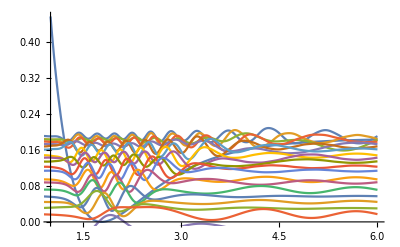

```mathematica
eigenPlot=Show[Plot[potentialFun[x],{x,1,L/2},PlotRange->Full],Plot[ Evaluate[0.02*eigxp+Energy],{x,0,L/2}]]
```

```mathematica
potentialEnergy=Table[NIntegrate[eigxp[[m]]* potentialFun[x]*eigxp[[m]],{x,-L/2,L/2}],{m,1,20}]
```

{0.15092,0.136517,0.170624,0.137265,0.160462,0.112319,0.107526,0.0913677,0.108931,0.102039,0.068776,0.0647489,0.0604328,0.0572489,0.0635458,0.0318717,0.0295533,0.0129688,0.0908326,0.0432064}

{0.0393507,0.0470348,0.0120829,0.0406262,0.0119382,0.055526,0.0534354,0.0561662,0.0337895,0.0323633,0.0536716,0.0488634,0.0337818,0.0309035,0.00758684,0.0251283,0.0147476,0.0170084,-0.0736215,-0.056789}

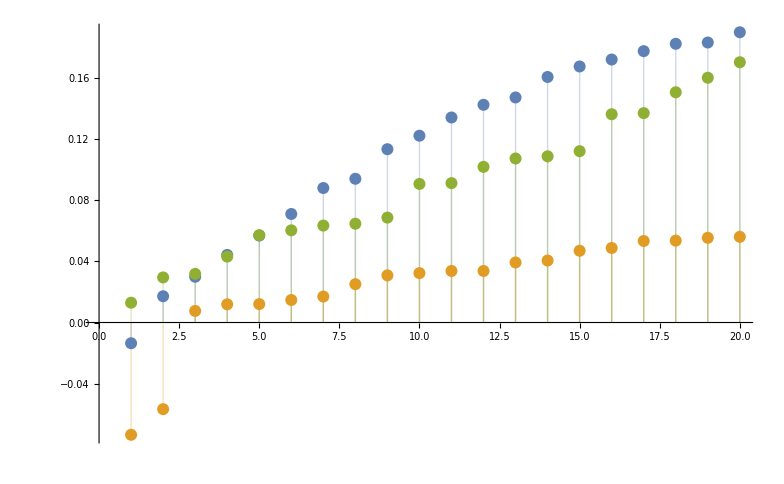

```mathematica
kineticEnergy=Table[Energy[[m]]-potentialEnergy[[m]],{m,1,20}]
Evaluate[ListPlot[{Sort[Energy],Sort[kineticEnergy],Sort[potentialEnergy]},Filling->Axis]]
```

```mathematica
β=1052.5822
averX=Table[NIntegrate[eigxp[[m]] x eigxp[[m]],{x,-L/2,L/2}],{m,1,20}]

ΔX=Table[Sqrt[NIntegrate[eigxp[[m]] x^2eigxp[[m]],{x,-L/2,L/2}]-averX[[m]]^2],{m,1,20}]
averP=Table[NIntegrate[eigxp[[m]] (-ⅈ *1728.16) *D[eigxp[[m]],x],{x,-L/2,L/2}],{m,1,20}]
ΔP=Table[Sqrt[NIntegrate[eigxp[[m]] *2*kineticEnerOperator[eigxp[[m]],x],{x,-L/2,L/2}]-averP[[m]]^2],{m,1,20}]
```

1052.58

{4.17581,3.63355,5.03079,3.70179,4.2742,3.03063,2.94269,2.69445,3.04758,2.9378,2.37627,2.34311,2.39866,2.28437,2.58286,1.88304,2.03817,1.77632,3.00805,2.11461}

{1.22178,1.10509,0.937878,1.16179,0.730304,0.955538,0.915023,0.882839,0.982478,0.772793,0.707495,0.652873,0.894659,0.788037,1.04271,0.404731,0.616034,0.326113,1.08008,0.647105}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.367}. NIntegrate obtained 0.-2.2979×10^-10 ⅈ and 2.58093×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.367}. NIntegrate obtained 0.-1.78535×10^-12 ⅈ and 3.59893×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.08575}. NIntegrate obtained 0.-1.16529×10^-12 ⅈ and 5.4954×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{0.-2.2979×10^-10 ⅈ,0.-1.78535×10^-12 ⅈ,0.-1.16529×10^-12 ⅈ,0.-5.97211×10^-12 ⅈ,0.-1.26536×10^-12 ⅈ,0.+2.329×10^-12 ⅈ,0.-4.30589×10^-12 ⅈ,0.+2.78533×10^-12 ⅈ,0.+2.21157×10^-12 ⅈ,0.+1.67554×10^-12 ⅈ,0.+2.04636×10^-12 ⅈ,0.-8.02345×10^-11 ⅈ,0.-3.33058×10^-11 ⅈ,0.-5.75493×10^-13 ⅈ,0.+7.48481×10^-13 ⅈ,0.+3.09086×10^-11 ⅈ,0.+1.41509×10^-12 ⅈ,0.+1.99663×10^-12 ⅈ,0.+5.86198×10^-14 ⅈ,0.-2.08531×10^-13 ⅈ}

{0.280283+0. ⅈ,0.30875+0. ⅈ,0.136788+0. ⅈ,0.285962+0. ⅈ,0.121868+0. ⅈ,0.33721+0. ⅈ,0.326822+0. ⅈ,0.343736+0. ⅈ,0.272175+0. ⅈ,0.23905+0. ⅈ,0.336342+0. ⅈ,0.311456+0. ⅈ,0.295175+0. ⅈ,0.272269+0. ⅈ,0.227671+0. ⅈ,0.246169+0. ⅈ,0.197475+0. ⅈ,0.136804+0. ⅈ,0.0878026+0. ⅈ,0.123553+0. ⅈ}

1.61822×10^6

1.30306×10^-6

204.4 k

6.17961×10^-7 (4.79047×10^-82 (0.00806492 Sin[1/12 π (6+x)]-0.0301688 Sin[1/6 π (6+x)]+0.0594213 Sin[1/4 π (6+x)]-0.0758984 Sin[1/3 π (6+x)]+139+0.00472515 Sin[33/4 π (6+x)]-0.000932404 Sin[25/3 π (6+x)])^2+1.23823×10^-84 (-0.00806917 Sin[1/12 π (6+x)]+0.00223168 Sin[1/6 π (6+x)]+152)^2+1.05034×10^-87 (-0.00965404 Sin[1]+150)^2+3.61196×10^-68 1^2+12+1+1.15962×10^-52 (1)^2+2.62914×10^-74 (147+0.000768415 Sin[1])^2+1.87384×10^-77 (156+0.000991931 Sin[25/3 π (6+x)])^2)
 |  |  |  |

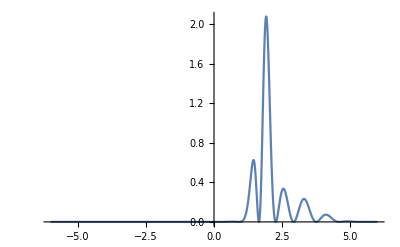

```mathematica
partitionFunc=Sum[Exp[-β Energy[[m]]],{m,1,20}]
EnsembleEnergy=Sum[Exp[-β Energy[[m]] Energy[[m]]]/partitionFunc,{m,1,20}]
heatCap=Sum[Quantity["BoltzmannConstant"] β^2  Energy[[m]]^2 Exp[-β Energy[[m]]],{m,1,20}]/partitionFunc
canonicalDistri=Sum[Exp[-β Energy[[m]] ]*eigxp[[m]]* eigxp[[m]],{m,1,20}]/partitionFunc
Evaluate[Plot[canonicalDistri,{x,-L/2,L/2},PlotRange->Full]]
```

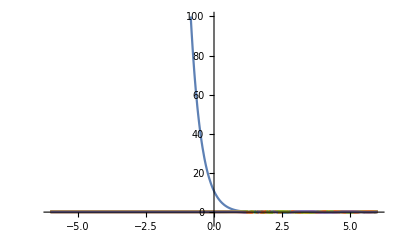

EigenFunction.jpg

Energy.txt

EnergyPlot.jpg

X_Fluctuation.txt

P_Fluctuation.txt

3.9802×10^-6

1.93309×10^-6

EnsembleEnergy.txt

HeatCapacity.txt

CanonicalLocationDistribution.jpg

```mathematica
Show[Plot[potentialFun[x],{x,-L/2,L/2},PlotRange->{-5,100}],Plot[ Evaluate[eigxp+Energy],{x,-L/2,L/2}]]
Export["EigenFunction.jpg",eigenPlot]
Export["Energy.txt",{Reverse[Energy],Reverse[kineticEnergy],Reverse[potentialEnergy]}]
Export["EnergyPlot.jpg",Evaluate[ListPlot[{Reverse[Energy],Reverse[kineticEnergy],Reverse[potentialEnergy]},Filling->Axis]]]
Export["X_Fluctuation.txt",Reverse[ΔX]]
Export["P_Fluctuation.txt",Reverse[ΔP]]
EnsembleKinetic=Sum[Exp[-β Energy[[m]] kineticEnergy[[m]]]/partitionFunc,{m,1,20}]
EnsemblePotential=Sum[Exp[-β Energy[[m]] potentialEnergy[[m]]]/partitionFunc,{m,1,20}]
Export["EnsembleEnergy.txt",{EnsembleEnergy,EnsembleKinetic,EnsemblePotential}]
Export["HeatCapacity.txt",heatCap]
Export["CanonicalLocationDistribution.jpg",Evaluate[Plot[canonicalDistri,{x,-L/2,L/2},PlotRange->Full]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["CanonicalLocationDistribution.jpg"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["CanonicalLocationDistribution.jpg"]]]
```

```mathematica
ScientificForm[partitionFunc]
```

1.61822×10^6

Part::pkspec1: The expression  cannot be used as a part specification.

$Aborted[]